# Clase #1: Métodos numéricos- Mathematica

## operaciones básicas

```mathematica
3+5
```

8

```mathematica
3 4(*el espacio es multiplicación*)
```

12

```mathematica
N[4000/3,12]
```

1333.33333333

```mathematica
N[ⅇ^2,100]
```

7.389056098930650227230427460575007813180315570551847324087127822522573796079057763384312485079121795

```mathematica
N[π,273]
```

3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534211706798214808651328230664709384460955058223172535940812848111745028410270193852110555964462294895493038196442881097566593344612847564823378678316527120190914564856692346034861045

```mathematica
Log[ⅇ^5]
```

5

```mathematica
N[Sin[90°]]
```

```mathematica
N[Cos[π/4]]
```

0.707107

```mathematica
Cos[π/4]
```

1/(√2)

## Operadores

```mathematica
Expand[(x+2)^3(x-1)^2]
```

x^5+4 x^4+x^3-10 x^2-4 x+8

```mathematica
Factor[x^2+2x+1]
```

(x+1)^2

```mathematica
Apart[(3x+2)/(x^3(x^2-1)(x^2+1))]
```

-2/x^3+(3-2 x)/(2 (x^2+1))-3/x^2+5/(4 (x-1))-1/(4 (x+1))

```mathematica
$PrePrint= TraditionalForm
```

TraditionalForm

```mathematica
D[3 x^3-5x ⅇ^(x^2),x]
```

-10 ⅇ^(x^2) x^2+9 x^2-5 ⅇ^(x^2)

```mathematica
FullSimplify[D[x y Sin[(ⅇ^(x z^3))/Log[z^2 Cos [x/z]]],z]]
```

(x y ⅇ^(x z^3) cos((ⅇ^(x z^3))/(log(z^2 cos(x/z)))) (3 x z^4 log(z^2 cos(x/z))-x tan(x/z)-2 z))/(z^2 log^2(z^2 cos(x/z)))

```mathematica
FullSimplify[D[x y Sin[(ⅇ^(x z^3))/Log[z^2 Cos [x/z]]],{z,2}]]
```

-1/(z^4 log^4(z^2 cos(x/z)))x y ⅇ^(x z^3) (ⅇ^(x z^3) sin((ⅇ^(x z^3))/(log(z^2 cos(x/z)))) (-3 x z^4 log(z^2 cos(x/z))+x tan(x/z)+2 z)^2-cos((ⅇ^(x z^3))/(log(z^2 cos(x/z)))) log(z^2 cos(x/z)) (log(z^2 cos(x/z)) (x^2-12 x z^5+3 x z^5 (3 x z^3+2) log(z^2 cos(x/z))+2 z^2)+x tan(x/z) (x tan(x/z) (log(z^2 cos(x/z))+2)+2 z ((1-3 x z^3) log(z^2 cos(x/z))+4))+8 z^2))

```mathematica
∫Sin[3x]ⅆx(*esc+intt+esc*)
```

-1/3 cos(3 x)

```mathematica
∫ⅇ^(-x^2)ⅆx
```

1/2 √π erf(x)

```mathematica
N[∫_0^∞ ⅇ^(-x^2)ⅆx,10]
```

0.8862269255

```mathematica
∫(3x+2)/(x^3(x^2-1)(x^2+1))ⅆx (*todo lo anterior con fracciones parciales*)
```

1/x^2-1/2 log(x^2+1)+3/x+5/4 log(1-x)-1/4 log(x+1)+3/2 tan^-1(x)

```mathematica
□
```

## Gráficas

### 2D

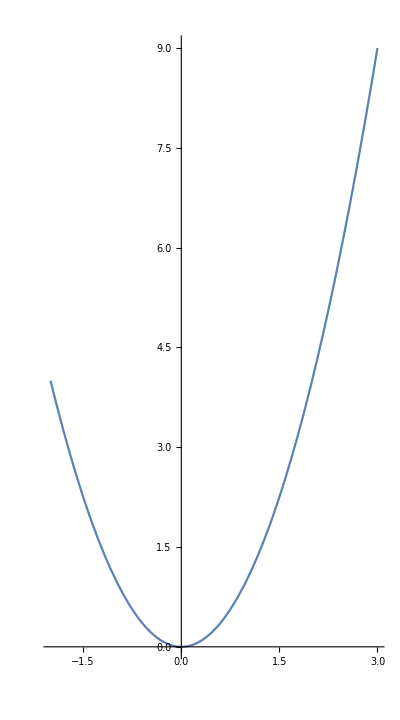

```mathematica
Plot[x^2, {x, -2,3},AspectRatio->9/5]
```

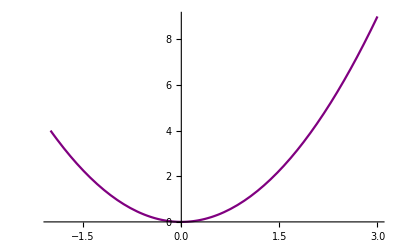

```mathematica
Plot[x^2, {x, -2,3},PlotStyle->Purple]
```

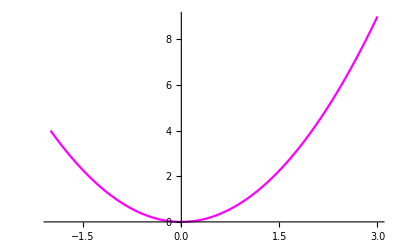

```mathematica
Plot[x^2, {x, -2,3},PlotStyle->RGBColor[1,0,1]]
```

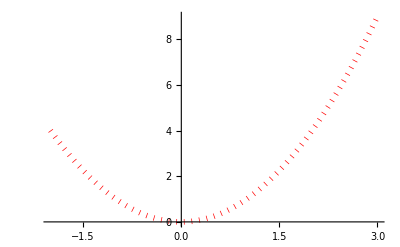

```mathematica
Plot[x^2, {x, -2,3},PlotStyle->Directive[Thickness[.01],Red, Dotted]]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π},PlotLabels->"Expressions", PlotStyle->Thick,ColorFunction->Function[{x,y},Hue[y]]]
```

-Graphics-

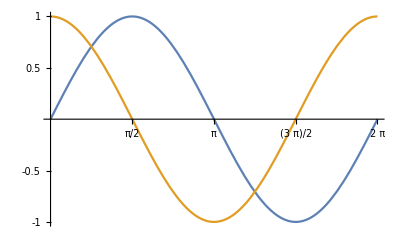

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}, Ticks->{{π/2,π,3/2 π,2π},{-1,-.5,.5,1}}]
```

```mathematica
Range[2,5]
```

{2,3,4,5}

```mathematica
Range[2,10,0.5]
```

{2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

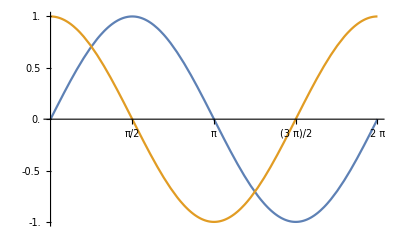

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}, Ticks->{{π/2,π,3/2 π,2π},Range[-1,1,0.5]}]
```

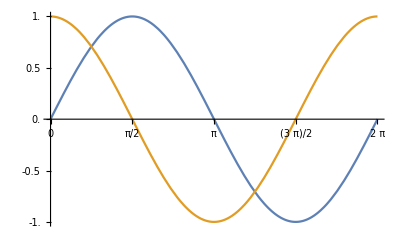

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2π}, Ticks->{Range[0,2π,π/8],Range[-1,1,0.5]}]
```